C1 (a) Define the scalar product .

```mathematica
ClearAll["Global`*"];

Clear[x, scalarProduct];

scalarProduct[f_,g_] :=
  Assuming[
  Element[x, Reals],
  FullSimplify[
  Integrate[Exp[-x^2] f g, {x, -Infinity, Infinity}]]];
```

(b) The Gram - Schmidt Procedure

```mathematica
Clear[gramSchmidt];

gramSchmidt[functions_List, innerProduct_] :=
  Module[{basis = {}, v},
    Do[
      v = FullSimplify[
        f - Total[(innerProduct[#, f]/innerProduct[#, #]) # & /@ basis]];
        
      v = FullSimplify[
        v/Sqrt[innerProduct[v, v]]];
        
      AppendTo[basis, v], {f, functions}];
    
    basis];
```

Then apply it to polynomials, with n = [Input integer]:

```mathematica
n = 2;

monomials = Table[x^k, {k, 0, n}];

polynomials = gramSchmidt[monomials, scalarProduct] // FullSimplify;
```

Display

```mathematica
TableForm[
  Table[{k, polynomials[[k+1]]}, {k, 0, n}],
  TableHeadings -> {None, {"k", "p_k(x)"}}
]
```

k | p_k(x)
0 | 1/π^(1/4)
1 | (√2 x)/π^(1/4)
2 | (√2 (-1/2+x^2))/π^(1/4)

(c) Use this program to check answer I calculated from question 4, n = 2

```mathematica
gramSchmidt[{1, x, x^2}, scalarProduct] // FullSimplify
```

{1/π^(1/4),(√2 x)/π^(1/4),(√2 (-1/2+x^2))/π^(1/4)}

Then verify orthonormality

```mathematica
ϕ = gramSchmidt[{1, x, x^2}, scalarProduct];

Table[
  FullSimplify[scalarProduct[ϕ[[i]], ϕ[[j]]]],
  {i, Length[ϕ]},
  {j, Length[ϕ]}
] // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

But how to apply this for n > 2 larger monomial lists???

(d) Approximate another function, use f(x) = cos(x) here.

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

Part::partd: Part specification p⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

Part::partd: Part specification p⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

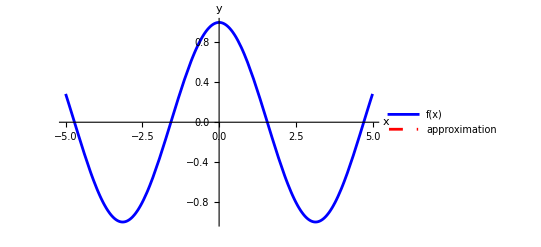

```mathematica
Clear[f, approximation];

f[x_] := Cos[x]

n = 10;
ϕ = gramSchmidt[Table[x^k, {k, 0, n}], scalarProduct];

coefficients = Table[FullSimplify[p[[k+1]], f[x]], {k, 0, n}];

approximation[x_] = FullSimplify[Sum[coefficients[[k+1]] p[[k+1]], {k, 0, n}]];

Plot[
  Evaluate[{f[x], approximation[x]},
  {x, -5, 5},
  PlotStyle->{Blue,{Red, Dashed}},
  PlotLegends->{"f(x)", "approximation"},
  AxesLabel->{"x", "y"},
  PlotRange->All]
]
```